Supplemental notebook to R. Herrmann, “Fractional Calculus - Introduction for Physicists”, 4th edition, World Scientific Publishing, Singapore. 
Chapter10
https://www.worldscientific.com/worldscibooks/10.1142/11107#t=aboutBook

# Riesz potential of a cuboid

Richard Herrmann

gigaHedron, r.herrmann@fractionalcalculus.org

October 2024.

## Introduction

Mathematica notebook presenting  solution to exercise 10.1

## Program

### start clean, try to integrate u

```mathematica
Clear[k,q,a1,a2,a3,tryV4Integral]
tryV4Integral = True;
Print[If[tryV4Integral,"trying to integrate the final 4th integral: f(u)=v3", "numerical integration of the 4th integral:  f(u)=v3"]]
```

trying to integrate the final 4th integral: f(u)=v3

### distance^2

```mathematica
d2=(x1-y1)^2+(x2-y2)^2+(x3-y3)^2;
```

### Gaussian integrand

```mathematica
v0=2/Sqrt[Pi] Exp[-u^kp d2];
```

### volume integration -> v3

```mathematica
v3=Integrate[v0,{x1,-a,a},{x2,-b,b},{x3,-c,c}]
```

1/4 π u^(-3 kp/2) (Erf[u^(kp/2) (a-y1)]+Erf[u^(kp/2) (a+y1)]) (Erf[u^(kp/2) (b-y2)]+Erf[u^(kp/2) (b+y2)]) (Erf[u^(kp/2) (c-y3)]+Erf[u^(kp/2) (c+y3)])

### try to solve the u-integral, but no simple solution

```mathematica
v4=If[tryV4Integral,Integrate[v3,{u,0,Infinity}]]
```

∫_0^∞ 1/4 π u^(-3 kp/2) (Erf[u^(kp/2) (a-y1)]+Erf[u^(kp/2) (a+y1)]) (Erf[u^(kp/2) (b-y2)]+Erf[u^(kp/2) (b+y2)]) (Erf[u^(kp/2) (c-y3)]+Erf[u^(kp/2) (c+y3)])ⅆu

### instead use f since v3 is a product

```mathematica
f[x_, a_, kp_] = (Erf[(a - x)*u^(kp/2)] + Erf[(a + x)*u^(kp/2)])/u^(kp/2)
```

u^(-kp/2) (Erf[u^(kp/2) (a-x)]+Erf[u^(kp/2) (a+x)])

### example

```mathematica
k = 3/2;
q = 2/3;
a1 = q/2;
a2 = 1/(2 q);
a3 = 1/2;
int1=f[x,a1,k]f[0,a2,k]f[0,a3,k];
int2=f[x,a1,k]f[y,a2,k]f[0,a3,k];
int3=f[x,a1,k]f[y,a2,k]f[z,a3,k];
```

### Pictures

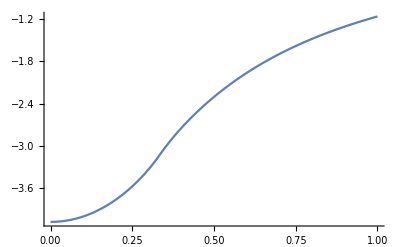

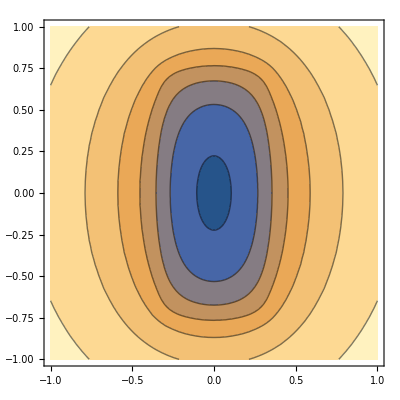

-Graphics3D-

-Graphics3D-

-Graphics-

```mathematica
blk=0.7;
t = ParallelTable[{x,y,z,-NIntegrate[int3,{u,0,Infinity}]},{x,-blk,blk,1/20},{y,-blk,blk,1/20},{z,-blk,blk,1/20}];
v = Flatten[t,2];

pic11 = Plot[-NIntegrate[int1,{u,0,Infinity}],{x,0,1}]
pic12= ContourPlot[-NIntegrate[int2,{u,0,Infinity}],{x,-1,1},{y,-1,1}]
pic21=Plot3D[-NIntegrate[int2,{u,0,Infinity}],{x,-1,1},{y,-1,1}]
pic22=ListContourPlot3D[v, Contours->3,Mesh->None]

result = GraphicsGrid[{{pic11,pic12},{pic21,pic22}}]
```

### Export and finish

```mathematica
Export["figure2x2.eps", result]
Export["figure2x2gray.eps", ColorConvert[result,"Grayscale"]]
```

figure2x2.eps

figure2x2gray.eps

figure2x2.eps

figure2x2gray.eps